```mathematica
data1={{{7.85297,45.48938},{7.85187,45.48936},{7.85186,45.48962},{7.85296,45.48964}},{{7.85241,45.49001},{7.85242,45.48950}}};
data2 ={{{7.85405,45.48914},{7.85295,45.48912},{7.85294,45.48938},{7.85404,45.48940}},{{7.85348,45.48977},{7.85349,45.48926}}} ;
poly1 = data1[[1]];
anchor1 = data1[[2]];
poly2 = data2[[1]];
anchor2 = data2[[2]];
```

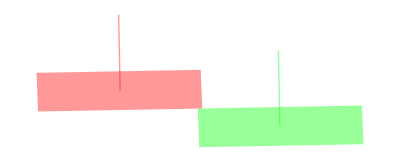

```mathematica
Graphics[{Opacity[0.4],Red,Polygon[poly1] ,Line[anchor1] , Green,Polygon[poly2], Line[anchor2]}]
```

# Top vs. Bottom

```mathematica
{{{7.85405,45.48914},{7.85295,45.48912},{7.85294,45.48938},{7.85404,45.48940}},{{7.85348,45.48977},{7.85349,45.48926}}
```

```mathematica
distance[{start_,end_},pt_]:=Module[{param=((pt-start).(end-start))/Norm[end-start]^2},EuclideanDistance[pt,start+Clip[param,{0,1}] (end-start)]];
angle[{x1_, y1_}, {x2_, y2_}] := -1 * ArcTan[y2-y1,x2-x1]
```

```mathematica
tl1 = poly1[[1]] ; tr1 = poly1[[2]] ; br1 = poly1[[3]] ; bl1 = poly1[[4]] ;
tl2 = poly2[[1]] ; tr2 = poly2[[2]] ; br2 = poly2[[3]] ; bl2 = poly2[[4]] ;
a1 = anchor1[[1]] ;c1 = anchor1[[2]] ;
a2 = anchor2[[1]] ; c2 = anchor2[[2]] ;
```

```mathematica
radTop1 = distance[{tl1, tr1}, a1] ;
radBottom1 = distance[{bl1, br1}, a1] ;
radTop2 = distance[{tl2, tr2}, a2] ;
radBottom2 = distance[{bl2, br2}, a2] ;
```

```mathematica
radBottom2
```

0.000380119

End Angle

```mathematica
r1 = radTop1 ; r2 = radBottom2 ;
gamma = angle[c1, c2]
gamma / Pi * 180
```

-1.79144

-102.642

```mathematica
rot = angle[a1, c1]
```

-3.12199

```mathematica
centerDist = EuclideanDistance[c1, c2]
```

0.00109659

```mathematica
beta=ArcSin[(r1-r2)/centerDist]
```

0.239339

```mathematica
alpha = gamma - beta ;
alpha += Pi / 2.0
```

-0.459986

```mathematica
r2
```

0.000380119

```mathematica
r1-r2
```

0.000259957

```mathematica
0.0004540626146252611
```

0.000454063

```mathematica
IntegerPart[0.0004540626146252611]
```

0

```mathematica
r1-r2
```

0.000259957